```mathematica
(*x: longitude of the sun*)
OpticalCorrection[x_]:=4* Sin[x] ^2    (*optical correction*)
RadialRaise[x_]:=-2* Cos[x]
Rotation[x_]:=Sin[x]
```

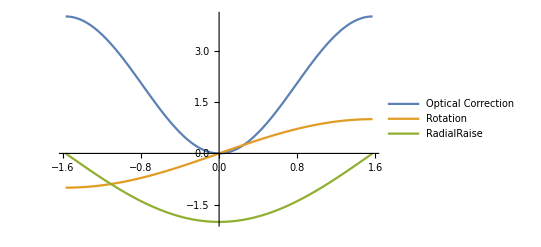

```mathematica
Plot[{OpticalCorrection[x],Rotation[x],RadialRaise[x]},{x,-Pi/2,Pi/2},PlotLegends->{"Optical Correction","Rotation","RadialRaise"}]
```

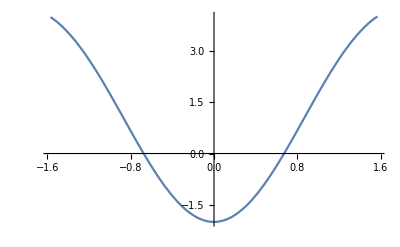

```mathematica
Plot[OpticalCorrection[x]+0.01*Rotation[x]+RadialRaise[x],{x,-Pi/2,Pi/2}]
```